```mathematica
ResourceFunction["MaTeXInstall"][]
```

ResourceObject::cloudc: You must connect to the Wolfram cloud to access the resource.

$Failed[]

```mathematica
Needs["PacletManager`"]
```

```mathematica
PacletInstall["/home/maksim/Downloads/MaTeX-1.7.5.paclet"]
```

Paclet[MaTeX,1.7.5,<>]

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["x^2+y^4=1",Magnification->2]
```

-Graphics-

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
ArrayReshape[Alphabet[][[;;6]],{2,3}]~Join~{{g,h,i}}
```

## Brownian Motion

A standard Brownian motion, or standard Wiener process, over [0,T]  is a random variable W_t that satisfies three properties:

W_0=0 with probability 1

For 0≤s<t≤T it’s the case that W_t - W_s ~ N(0,t-s) ~ √(t-s)N(0,1)

For 0≤s<t<u<v≤T the increments  W_t-W_s and W_u-W_v are independent

Consider discretized Brownian motion: let δt=T/N and j·δt. Conditions 2 and 3 imply

W_j=W_(j-1)+ⅆ W_j

where each ⅆW_j~√δtN(0,1).

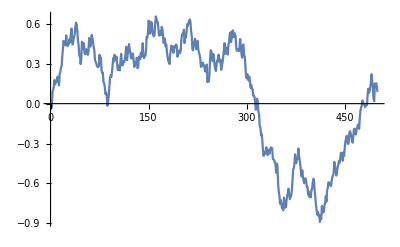

```mathematica
ND :=RandomVariate[NormalDistribution[]];
T=1;n=500;δt=T/n;
dW = ConstantArray[0,n];
W=ConstantArray[0,n];
W[[1]]=√δt ND;
For[j=2,j≤n,j++,
	dW=√δt ND;
	W[[j]]=W[[j-1]]+dW;
];

ListLinePlot[W]
```

Vectorized calculations

```mathematica
dW = RandomVariate[NormalDistribution[],n];
```

```mathematica
W=Accumulate[dW];
```

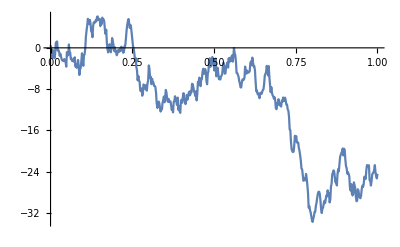

```mathematica
ListLinePlot[MapThread[{#1,#2}&,{Array[#&,n,{0,T}], W}]]
```

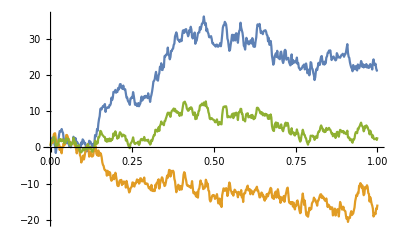

```mathematica
M=2;
dW = RandomVariate[NormalDistribution[],{n,M}];
W=Accumulate[dW];
m=Mean[W//Transpose];
((W//Transpose)~Join~{m})//Transpose;
dts=Array[#&,n,{0,T}];
plots=Map[MapThread[Function[{p2,p3},{p2,p3}],{dts,#1}]&,((W//Transpose)~Join~{m})];
ListLinePlot[plots]
```